```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

## Plot potentials

```mathematica
uscan=Join[Table[i,{i,1/10,9/10,1/10}],{99/100}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100}

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ReVsu"<>ToString[Round[100uscan[[n]]]]<>"T250u.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ReVcu"<>ToString[Round[100uscan[[n]]]]<>"T250u.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ImVcu"<>ToString[Round[100uscan[[n]]]]<>"T250u.dat"]];data=Append[data,{20000,data[[-1,2]]}];
data=Transpose[{data[[All,1]],EstimatedBackground[data[[All,2]]]}];ImVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]-1}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ImVsu"<>ToString[Round[100uscan[[n]]]]<>"T250u.dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]-1}]];
```

```mathematica
uSetS={"1/10","2/10","3/10","4/10","5/10","6/10","7/10","8/10","9/10","99/100","Vac"};
```

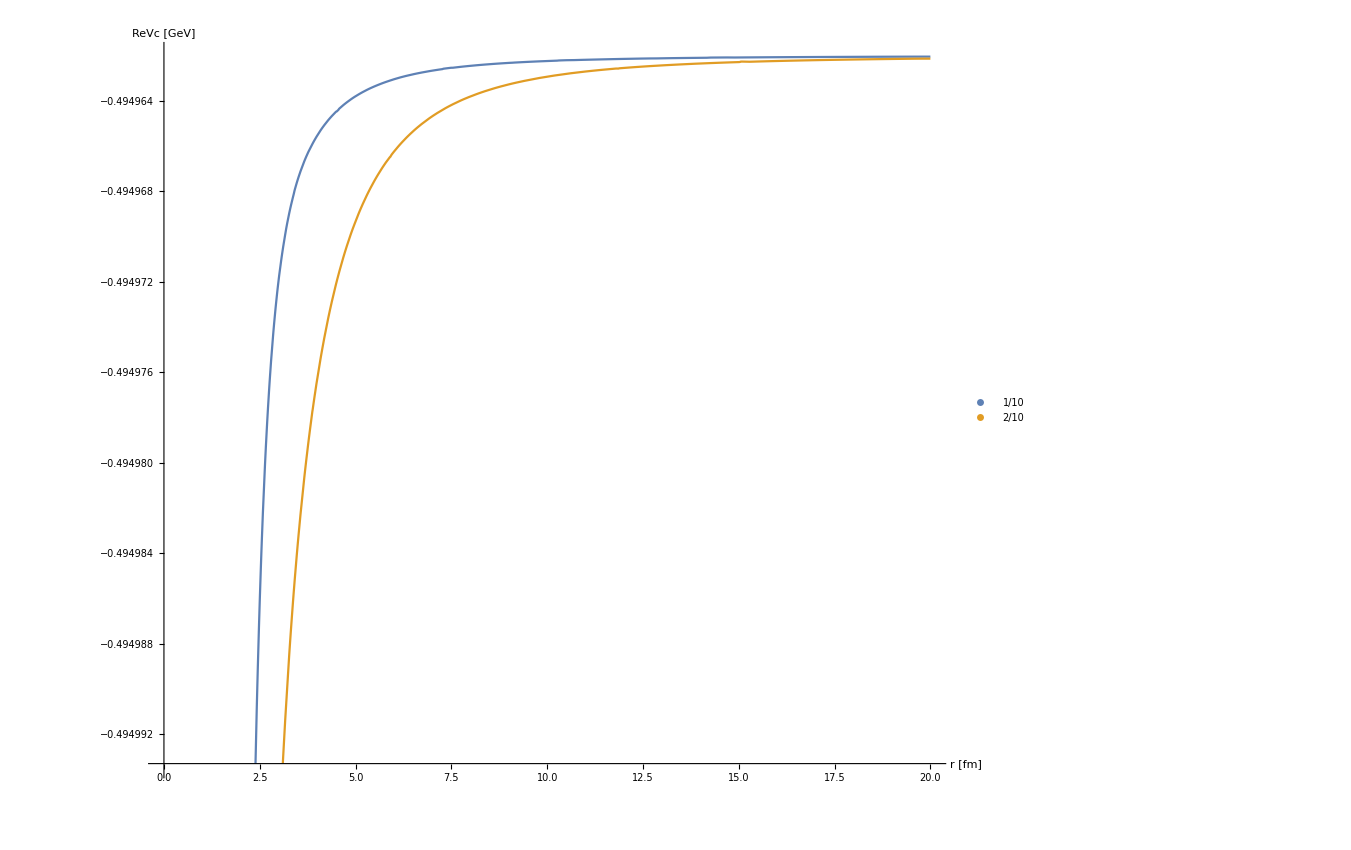

```mathematica
Plot[{ReVcu[1][r/0.197],ReVcu[2][r/0.197]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.2}],BaseStyle->{FontSize->14}]
```

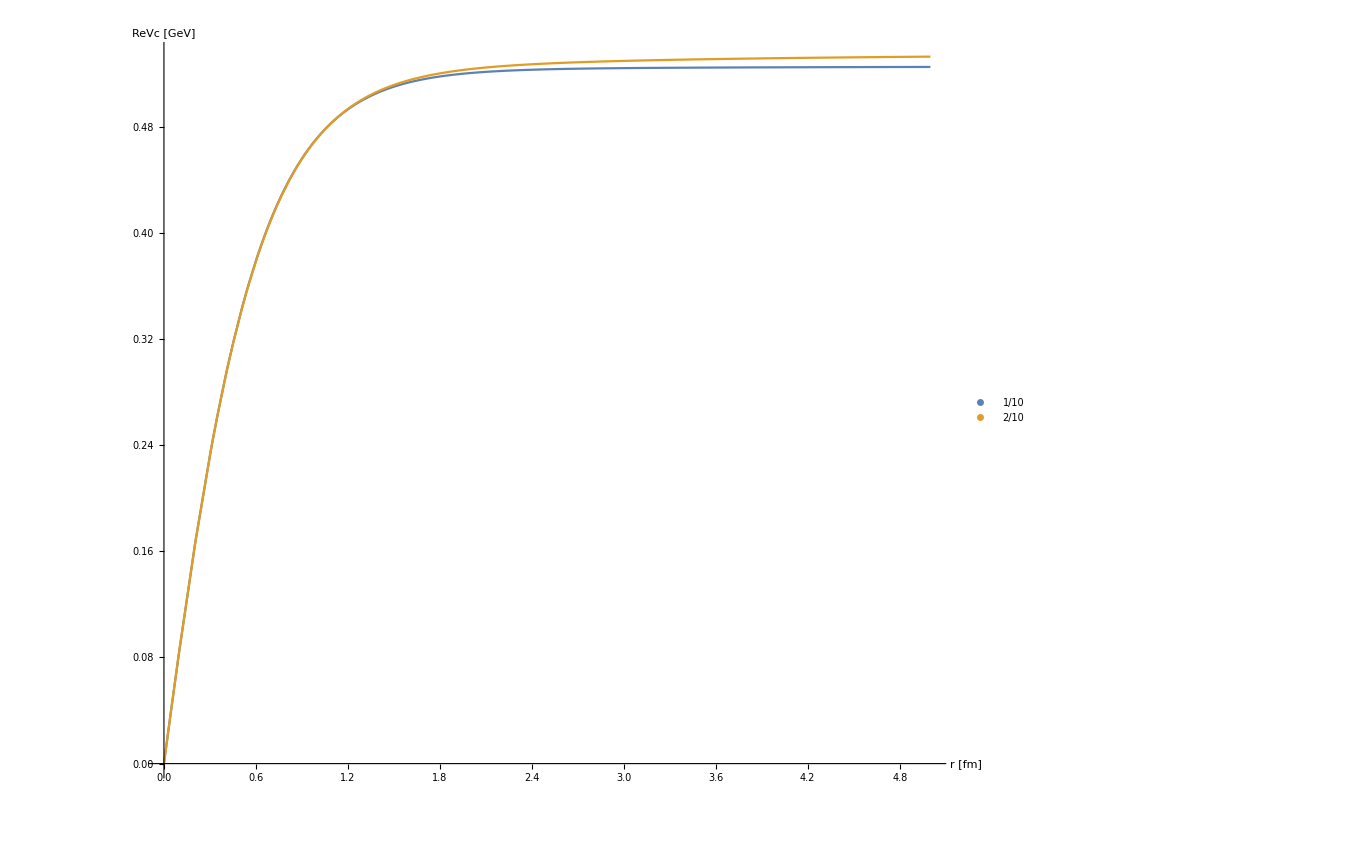

```mathematica
Plot[{ReVsu[1][r/0.197],ReVsu[2][r/0.197]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.4}],BaseStyle->{FontSize->14},PlotRange->All]
```

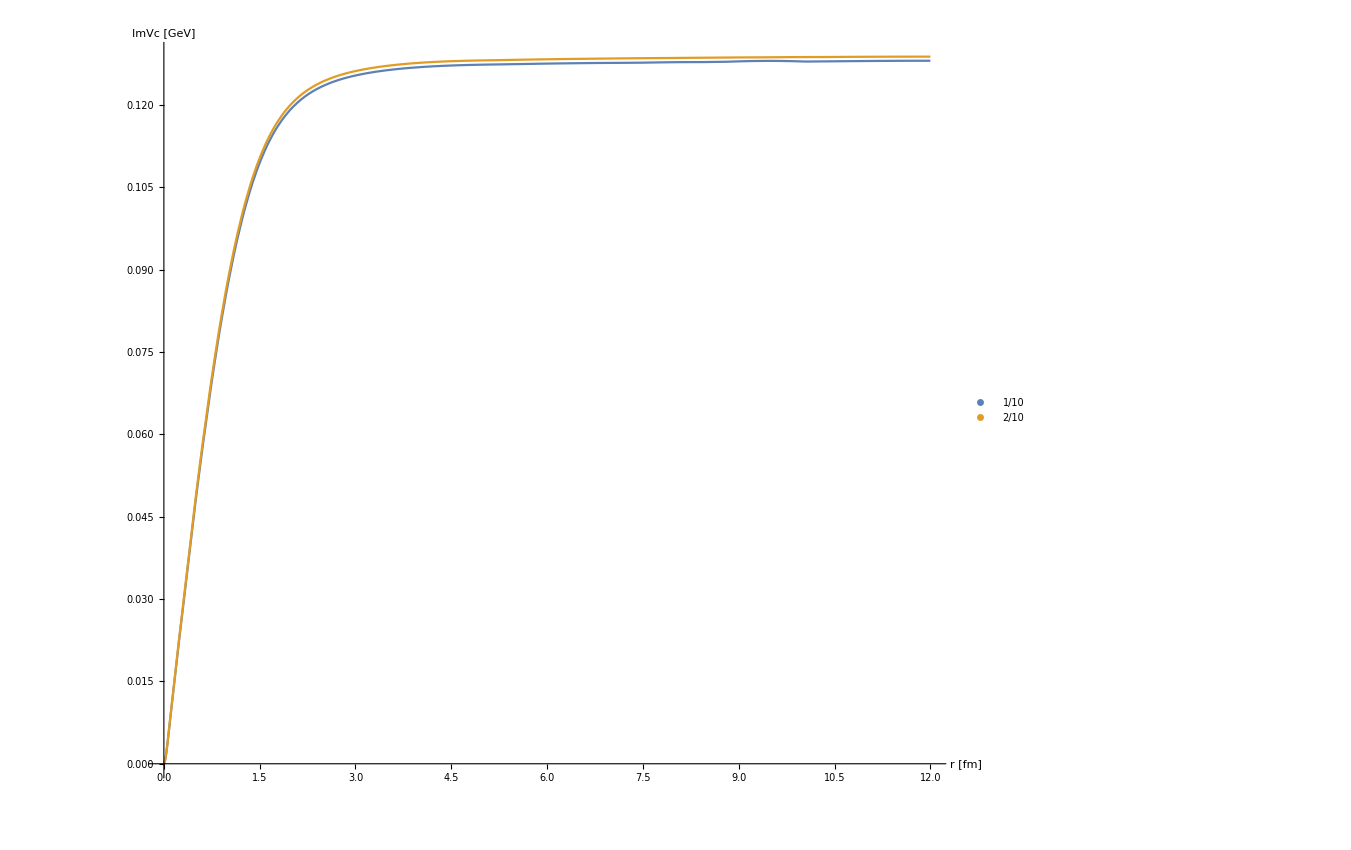

```mathematica
Plot[{Re[ImVcu[1][r/0.197]],Re[ImVcu[2][r/0.197]]},{r,1/1000,12},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14},PlotRange->All]
```

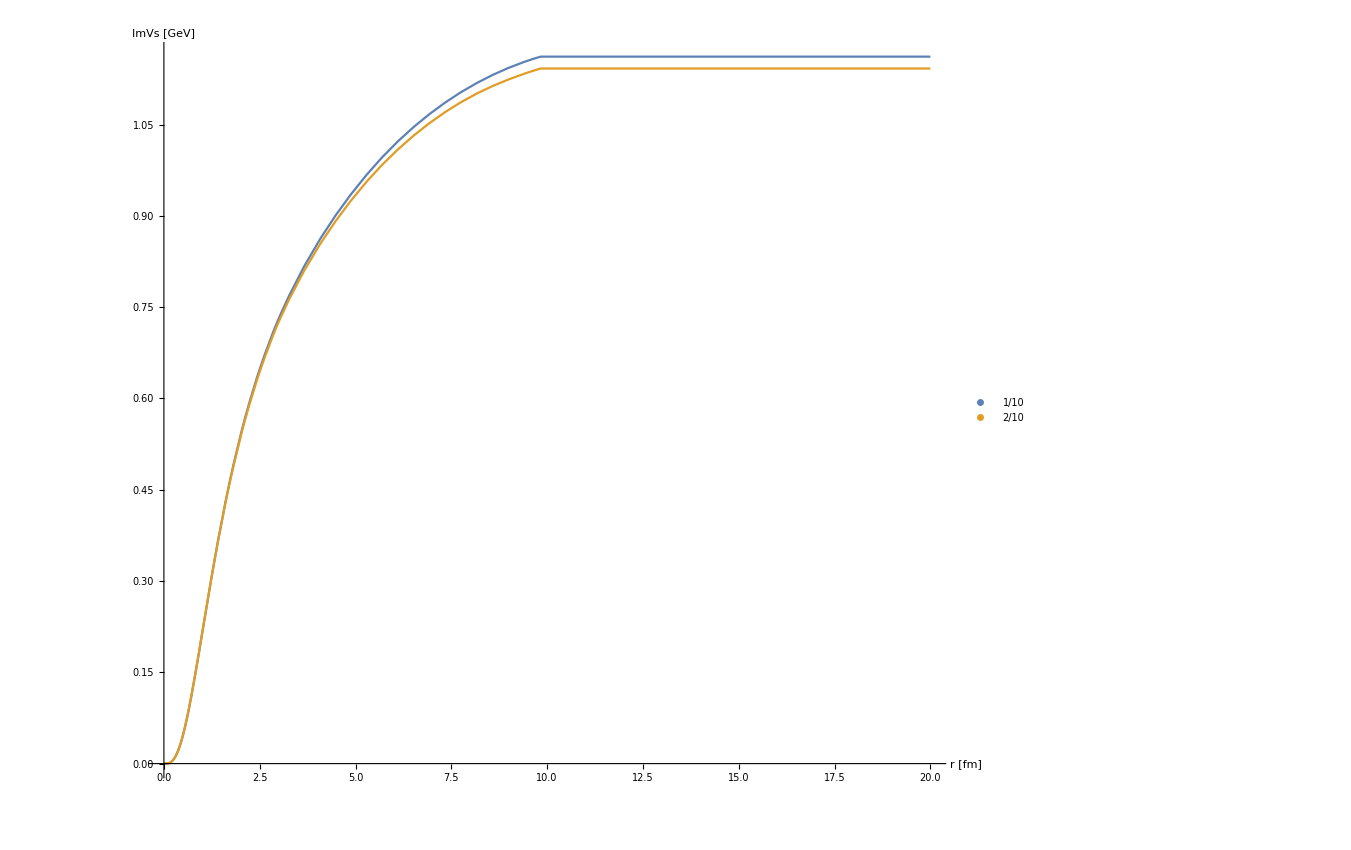

```mathematica
Plot[{Re[ImVsu[1][r/0.197]],Re[ImVsu[2][r/0.197]]},{r,1/1000,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

## Spectra

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

```mathematica
Nc=3;
```

#### Charmonium s-wave

```mathematica
swaveccspectra[u_]:=Block[{α=αcont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->15,MaxSteps->1000000];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc_perp/swccu"<>ToString[Round[10u]]<>"spectraT250u.dat",Sort[ccss]];
];
```

```mathematica
swavebbspectra[u_]:=Block[{α=αcont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb_perp/swbbu"<>ToString[Round[10u]]<>"spectraT250u.dat",Sort[ccss]];
];
```

```mathematica
swaveccspectra[1]//AbsoluteTiming
```

```mathematica
swavebbspectra[1]//AbsoluteTiming
```

{148.721,Null}

```mathematica
check=ToExpression[Import["cc_perp/swccu"<>ToString[Round[10]]<>"spectraT250u.dat"]];
```

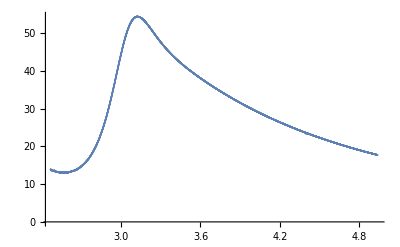

```mathematica
ListPlot[check[[1800;;]]]
```